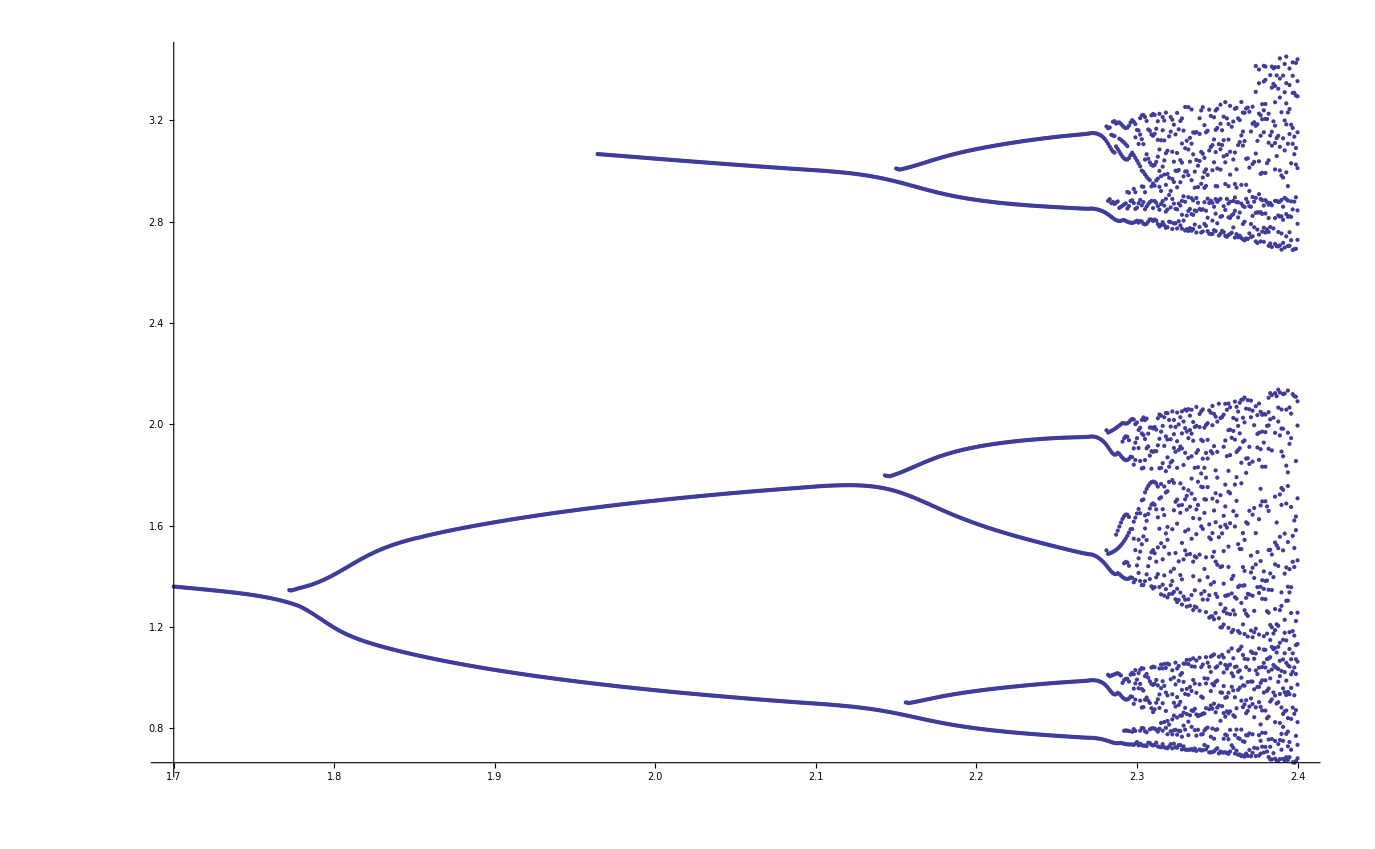

```mathematica
G=3.55;ω=2*Pi*12*10^6;
(*s=ParametricNDSolveValue[{
v'[t]==2*G*BesselJ[1,v[t-τ]] Cos[ω*τ]-v[t],
v[t/;t≤0]==0.001},
{v,v'},
{t,0,120},{τ}];
Manipulate[ParametricPlot[{s[τ][[1]][t],s[τ][[2]][t]},{t,60,120},AxesLabel->{v,v'},AspectRatio->1],{{τ,2},1,4}]*)

tab=Table[{sol,points}=Reap@NDSolveValue[{
v'[t]==2*G*BesselJ[1,v[t-τ]] Cos[ω*τ]-v[t],
v[t/;t≤0]==0.001,
WhenEvent[v'[t]>0,
If[t>150,Sow[v[t]]]]},
{v,v'},{t,0,250}];
{τ,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.05&)],{τ,1.7,2.4,.001}];
ListPlot[Flatten[tab,1]]
```